```mathematica
Get["/Users/beto/Documents/Wolfram Mathematica/Base/Alpha/Alpha.m"]
```

```mathematica
cm05={{0,1,0,1,1},{1,0,1,1,0},{1,1,0,0,0},{1,0,0,0,1},{1,0,1,1,0}};

dyn05={"AND","OR","OR","AND","OR"};

mem05=calculatingAttractors4Partition[{1,2,3,4,5},{"AND","OR","OR","AND","OR"},cm05]//AbsoluteTiming;

ser05=calculatingAttractors4PartitionInSerie[{1,2,3,4,5},{"AND","OR","OR","AND","OR"},cm05]//AbsoluteTiming;

mem05[[1]]
ser05[[1]]
Equal[mem05[[2]],ser05[[2]]]
mem05[[2]]
ser05[[2]]

runDynamic[cm05,dyn05]["RepertoireOutputs"]//MatrixForm
```

0.02322

0.014538

False

<|AllDecimalRepresentations→<|{0,0,0,0,0}→{0,16},{0,0,1,0,0}→{2,18},{0,1,0,0,1}→{4,8,12,20,24,28},{0,1,1,0,1}→{1,5,3,6,7,9,13,10,11,14,15,22},{1,1,1,0,1}→{26,30},{0,1,1,1,1}→{17,21,19,23,25,29},{1,1,1,1,1}→{27,31}|>,AllSumandos→<|{0,0,0,0,0}→{0},{0,0,1,0,0}→{0},{0,1,0,0,1}→{0},{0,1,1,0,1}→{0},{1,1,1,0,1}→{0},{0,1,1,1,1}→{0},{1,1,1,1,1}→{0}|>|>

<|AllDecimalRepresentations→<|{0,0,0,0,0}→{0,16},{1,1,1,1,1}→{27,31},{0,1,1,1,1}→{17,21,19,23,25,29},{0,0,1,0,0}→{2,18},{1,1,1,0,1}→{26,30},{0,1,1,0,1}→{1,5,3,6,7,9,13,10,11,14,15,22},{0,1,0,0,1}→{4,8,12,20,24,28}|>,AllSumandos→<|{0,0,0,0,0}→{0},{1,1,1,1,1}→{0},{0,1,1,1,1}→{0},{0,0,1,0,0}→{0},{1,1,1,0,1}→{0},{0,1,1,0,1}→{0},{0,1,0,0,1}→{0}|>|>

(0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 1
0 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1)

```mathematica
cm16={{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1},{1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,1,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0}};

dyn16={"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","AND","OR","AND"};


(*findIndexesOfOutputs4Mechanism[{5,7,9,10},{1,1,1,0},dyn16,cm16]
findPattInInputsPhiStyle[{1,2,3,4,5},{0,0,0,0,0},16];*)

mem=calculatingAttractors4Partition[{1,2,3,4,5,6,7,8,9,10},{"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND"},cm16]//AbsoluteTiming;

ser=calculatingAttractors4PartitionInSerie[{1,2,3,4,5,6,7,8,9,10},{"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND"},cm16]//AbsoluteTiming;

mem[[1]]
ser[[1]]
Equal[mem[[2]],ser[[2]]]
mem[[2]]
ser[[2]]
```

13.9539

13.9528

False

```mathematica
joinedNames= {9, 11, 15, 4, 10, 14, 16, 3, 6, 1, 12}
cc=Complement[Range[Length[cm16]],joinedNames]
ss =2^#&/@(cc-1)
sum=2^#&/@((Complement[Range[Length[cm16]],joinedNames])-1)
s=Distribute[{{},{#}}&/@sum,List,List,List,Union]//Sort (*This is the same than Subsets*)
Subsets[sum]
```

```mathematica
cm16={{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1},{1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,1,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0}};

dyn16={"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","AND","OR","AND"};
catts=calculatingAttractors4Partition[{1,2,3,4,5},dyn16,cm16];
catts2=calculatingAttractors4Partition[{6,7,8,9,10},dyn16,cm16];
catts3=calculatingAttractors4Partition[{11,12,13,14,15},dyn16,cm16];

dr=catts["AllDecimalRepresentations"]//TableForm
dr2=catts2["AllDecimalRepresentations"]//TableForm
dr3=catts3["AllDecimalRepresentations"]//TableForm

(*findIndexesOfOutputs4Mechanism[{1,2,3,4},{1,1,0,0},{"AND","OR","OR","AND"},cm16];*)
```

```mathematica
cs = {0,0,0,0,0};
emdDir="/Users/beto/WolframWorkspaces/Base/Alpha/EMD";
nodesSys = Range[Length[cm05]];

Needs["JLink`"];

InstallJava[];
SetDirectory[emdDir];
AddToClassPath[emdDir];

testClass=LoadJavaClass["Aux2"];
obj=JavaNew[testClass];

matrixResults = List[];

(*validMechas=createValidMechanisms[cm05]["ValidMechanisims"]*)
mechanisms=Delete[Subsets[nodesSys],1];

futUnconstrProbByBit05=calcFullBitUnconstrProbInOutputs[cm05,dyn05]["UnconstrProbbsByBit"];

(*Print["MECHANISMS: "<> ToString[mechanisms]];*)

For[b=1, b≤Length[mechanisms], b++,


oneMecha = Part[mechanisms,b];
If[Length[oneMecha]>1,subCS = Extract[cs,Split[oneMecha]],subCS = Extract[cs,oneMecha]];

If[Length[subCS]>1, subCS = subCS, subCS =  List[subCS]];

(* begin -----------------*)
(*Print["[][][][][][][][][][]"];
Print["Mecha: "<> ToString[oneMecha]<> " SCS: "<> ToString[subCS]];*)
(*  end -----------------*)

For[c=1, c≤ 3(*Length[mechanisms]*),c++,

vectorResults = List[];
onePurview = Part[mechanisms,c];




pPD = createPastProbabilityDistribution[oneMecha,subCS,onePurview,dyn05,cm05]["ProbabilityDistribution"];

fPD = createFutureProbabilityDistribution[oneMecha,subCS,onePurview,dyn05,cm05,futUnconstrProbByBit05]["ProbabilityDistribution"];

(* begin -------------------------*)
(*Print["Past probability distribution: "<> ToString[pPD]];
Print["Future probability distribution: "<> ToString[fPD]];
(*  end -------------------------*)*)


pastDist = obj@emdDist[pSysProbbDistr,pPD,2];
futDist =  obj@emdDist[fSysProbbDistr,fPD,2];

vectorResults = AppendTo[vectorResults,oneMecha];
vectorResults = AppendTo[vectorResults,onePurview];
vectorResults = AppendTo[vectorResults,pastDist];
vectorResults = AppendTo[vectorResults,futDist];
matrixResults = AppendTo[matrixResults, vectorResults];

(* begin -----------------*)
(*Print["   -----------------------------------"];
Print["  Purview: "<> ToString[onePurview]];
Print["  Distributions: "];
Print[pPD];
Print[fPD];
Print["  PastDist: "<> ToString[pastDist]<> " FutDist: "<> ToString[futDist]];*)
(*  end -----------------*)

];

];
```

```mathematica
matrixResults//MatrixForm
```

```mathematica
cs = {0,0,0,0,0};
emdDir="/Users/beto/WolframWorkspaces/Base/Alpha/EMD";
calculateIIAllPartitions[cs,emdDir,dyn05,cm05,uv05,atts05,positions05,pSysProbbDistr,fSysProbbDistr]
```

```mathematica
mechanism = {1,2,3};
substate = {0,0,0};
purview = {1,3};

inputsFound=findPattInInputsPhiStyle[mechanism,substate,Length[cm05]]["Locations"]
inputsFound = inputsFound-1
ins=setInputsToBinPhiStyle[Length[cm05],inputsFound]
(*Table[calculateOneOutptuOfNetwork[Part[ins,w],cm05,dyn05]["Output"],{w,1,Length[ins],1}]*)
Table[Part[calculateOneOutptuOfNetwork[Part[ins,w],cm05,dyn05]["Output"],purview],{w,1,Length[ins],1}]
```

```mathematica
findPattInInputsPhiStyle[{1,2,3},{0,0,0},5]
```

<|Locations→{1,9,17,25}|>

```mathematica
cm16={{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1},{1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,1,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0}};

dyn16={"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","AND","OR","AND"};

findIndexesOfOutputs4Mechanism[{5,7,9,10},{0,0,1,0},{"OR","AND","OR","AND"},cm16]
```

```mathematica
16 nodes

cm16={{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1},{1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,1,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0}};
dyn16={"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","AND","OR","AND"};

ff16=calculatingPattsInDivisionsOfCM[cm16,dyn16,4];
locations16 = ff16["Locations"];
sumandos16 = ff16["Sumandos"];
ByteCount[ff16]

Timing[cca16=calculatingAttractors[locations16,sumandos16]]
atts16=cca16["AttractorsByPosition"];
atts=Keys[atts16];
Print["Number of differente attractors: "<> ToString[Length[atts16]]];
N[4/551]
Length[Flatten[Values[atts16]]]
ByteCount[atts16]
First[atts16]
```

```mathematica
runLengthEnconding[atts16]["Encoding"]
```

Keys::invrl: The argument atts16 is not a valid Association or a list of rules.

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

ReplacePart::pkspec1: The expression 1+atts16[atts16[atts16]] cannot be used as a part specification.

Delete::partw: Part 1 of atts16 does not exist.

{{0,1}}

```mathematica
cm16={{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1},{1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,1,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0}};
dyn16={"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","AND","OR","AND"};
findIndexesOfOutputs4Mechanism[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},dyn16,cm16]
findIndexesOfOutputs4Mechanism[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0},dyn16,cm16]
```

<|AllInputNodes→{7,13,3,6,10,14,16,9,15,1,5,12,11,2,4,8},DecimalRepertoire→{0,128,16,144},Sumandos→{0}|>

<|AllInputNodes→{7,13,3,6,10,14,16,9,15,1,5,12,11,2,4,8},DecimalRepertoire→{8,136,24,152},Sumandos→{0}|>

```mathematica
cm20={{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0,0,1,0},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1,1,0,0,0},{1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,1,0,0,0,1,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1},{0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0},{1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0}};
dyn20={"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","AND","OR","AND","AND","OR","OR","AND"};

ff20=calculatingPattsInDivisionsOfCM[cm20,dyn20,4];
locations20 = ff20["Locations"];
sumandos20 = ff20["Sumandos"];
ByteCount[ff20];
```

```mathematica
Timing[cca20=calculatingAttractors[locations20,sumandos20]]
```

```mathematica
atts20=cca20["AttractorsByPosition"];
Length[Flatten[Values[atts20]]]
ByteCount[atts20]
```

1048576

9288840

```mathematica
cm26={{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,1,0,0,0,1,0,0,1,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,1,0,0,1,0,1,0,1,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0,0,1,0,0,1,0,0,0,0},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,1,0,1,0,1,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,1,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,1,0,0,0,1,0,0,1,1,0,0,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,1,1},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0},{1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,0,0,0},{1,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,1,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0}};
dyn26={"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","AND","OR","AND","AND","OR","OR","AND","OR","OR","AND","AND","AND","OR"};

ff26=calculatingPattsInDivisionsOfCM[cm26,dyn26,2];
locations26 = ff26["Locations"];
sumandos26 = ff26["Sumandos"];
bc26=ByteCount[ff26]
Timing[cca26=calculatingAttractors[locations26,sumandos26]]
atts26=cca26["AttractorsByPosition"];
Length[Flatten[Values[atts26]]]
ByteCount[atts26]
```

125423584

67108864

```mathematica
findPattInInputsPhiStyle[{1,2,3,4,5},{0,0,0,0,0},16]
```

```mathematica
16 nodes

cm16={{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1},{1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,1,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0}};
dyn16={"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","AND","OR","AND"};
cs16={0,0,1,0,1,1,0,1,0,0,1,0,0,0,1,0};

unconstrDistros16 = computeUnconstrainedDistros[cm16,dyn16,cs16,{0,0,0,0,0}];
pastUnconstrDistr16 = unconstrDistros16["UnconstrPastProb"]
futUnconstrDistr16 = unconstrDistros16["UnconstrFutProb"]
fbupo16 = unconstrDistros16["bitProbDistro4Outs"]
```

16 nodes

<|1→{0.75,0.25},2→{0.03125,0.96875},3→{0.125,0.875},4→{0.96875,0.03125},5→{0.125,0.875},6→{0.25,0.75},7→{0.96875,0.03125},8→{0.0625,0.9375},9→{0.03125,0.96875},10→{0.9375,0.0625},11→{0.25,0.75},12→{0.125,0.875},13→{0.875,0.125},14→{0.75,0.25},15→{0.0625,0.9375},16→{0.875,0.125}|>

```mathematica
Euclidian disntace between two distros in Run-Length coding
```

```mathematica
d1={{0.037037,6},{0.00925926,2},{0.037037,6},{0.00925926,2},{0.037037,6},{0.00925926,2},{0.037037,6},{0.00925926,2}};

d2= {{0.037037,6},{0.00925926,2},{0.037037,6},{0.00925926,2},{0.037037,6},{0.00925926,2},{0.037037,6},{0.00925926,2}};

distanceRunLengthEnconde[d1,d2]
```

<|EuclidianDistance→0.|>

```mathematica
Using EMD from libraries
```

```mathematica
emdDir="/Users/beto/WolframWorkspaces/Base/Alpha/EMD";

Needs["JLink`"];

InstallJava[];
SetDirectory[emdDir];
AddToClassPath[emdDir];

testClass=LoadJavaClass["Aux2"];
obj=JavaNew[testClass];
d1= {0.166667, 0.0833333, 0.166667, 0.0833333, 0.166667, 0.0833333, 0.166667, 0.0833333};
d2= {0.333333, 0., 0., 0.333333, 0.333333, 0., 0., 0.};

a0={0.16666666666666666,0.08333333333333333,0.16666666666666666,0.08333333333333333,0.16666666666666666,0.08333333333333333,0.16666666666666666,0.08333333333333333};
a1={0.3333333333333333,0,0,0.3333333333333333,0.3333333333333333,0,0,0};
d9={0.3333333333333333,0.,0.,0.3333333333333333,0.3333333333333333,0.,0.,0.};
d10={0.16666666666666666,0.08333333333333333,0.16666666666666666,0.08333333333333333,0.16666666666666666,0.08333333333333333,0.16666666666666666,0.08333333333333333};
d11={0.166667, 0.166667, 0.166667, 0.166667, 0.166667, 0., 0.166667, 0.};

d12= {0.,0.,0.,0,1.,0.,0.,0.};
d13= {0,0,0,0,0.9,0,0.1,0};

d14= {0.667,0,0,0.333};
d15={0.8, 0, 0, 0.2};

d16={0.,0.,0.75,0.25};
d17={0.,0.,0.9,0.1};

Timing[pyEMD[d16,d17]]
Timing[EMD[d16,d17]]

(*
Methods[obj];

obj@emdDist[d9,d11,2]
obj@emdDist[d9,d11]
EMD[d13,d12]
*)
```

{0.013043,<|Distance→0.15|>}

{0.543886,<|Distance→0.15|>}

```mathematica
Test loading JAVA clases for EMD
```

```mathematica
emdDir="/Users/beto/WolframWorkspaces/Base/Alpha/EMD";

Needs["JLink`"];

InstallJava[];
SetDirectory[emdDir];
AddToClassPath[emdDir];

testClass=LoadJavaClass["Aux2"];
obj=JavaNew[testClass];

a1={0,0,1,0};
a2={0.5,0,0.5,0};

Methods[obj];

obj@emdDist[a1,a2]
```

```mathematica
num=ToExpression[Import["!python3 /Users/beto/WolframWorkspaces/Base/Alpha/run_pyphi_emd.py 2 0.3333,0.1667,0.3333,0.1667 0.66667,0,0,0.33333 2>&1","Text"]]
```

0.5

```mathematica
ArrayReshape[TensorProduct[{0.25,0.25,0.25,0.25},{0.5,0.5}],{2,2,1}]
```

{{{0.125},{0.125}},{{0.125},{0.125}}}

```mathematica
Testing some results of Tononis with Alpha (Figure 8)
```

```mathematica
cm03={{0,1,1},{1,0,1},{1,1,0}};
dyn03={"OR","AND","XOR"};
cs03={1,0,0};
unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
pastUnconstrDistr = unconstrDistros["UnconstrPastProb"];
futUnconstrDistr = unconstrDistros["UnconstrFutProb"];

mechaPivot = {2,3};
purPivot = {1,2,3};
scsP = {0,0};

pastMecha = {1,2,3};
pastPurview = {1};
scs = {1,0,0};

pastMechaC = {1,2,3};
pastPurC = {1};
scsC = {1,0,0};

pastWSDistro = createPastProbabilityDistribution[mechaPivot,scsP,purPivot,dyn03,cm03]["ProbabilityDistribution"];

(*BC/A*)

(*when mecha={} it returs distribution of reference*)
(*when purview={} returns 1*)
If[pastMecha === {}, uno = pastUnconstrDistr];
If[pastPurview === {}, uno = 1;]
If[(pastMecha ≠ {})&& (pastPurview≠ {}),
uno=createPastProbabilityDistribution[pastMecha,scs,pastPurview,dyn03,cm03]["ProbabilityDistribution"];
];

If[pastMechaC === {}, dos = pastUnconstrDistr];
If[pastPurC === {}, dos = 1;]
If[(pastMechaC ≠ {})&& (pastPurC≠ {}),
dos=createPastProbabilityDistribution[pastMechaC,scsC,pastPurC,dyn03,cm03]["ProbabilityDistribution"];
];

tres = uno * dos;

Print[uno];
Print[dos];
Print[tres];
obj@emdDist[pastUnconstrDistr,tres]
```

{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125}

{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125}

{0.015625,0.015625,0.015625,0.015625,0.015625,0.015625,0.015625,0.015625}

6.125

```mathematica
cm03={{0,1,1},{1,0,1},{1,1,0}};
dyn03={"OR","AND","XOR"};
cs03={1,0,0};
allOptions={0,0,0,0,0};
unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
fbupo = unconstrDistros["bitProbDistro4Outs"]
unconstrainedFutPartitionedDistro[{2,3},fbupo]
```

<|1→{0.25,0.75},2→{0.75,0.25},3→{0.5,0.5}|>

<|UnconstrainedPastPartitionedDistro→{0.375,0.125,0.375,0.125}|>

```mathematica
cm03={{0,1,1},{1,0,1},{1,1,0}};
dyn03={"OR","AND","XOR"};
cs03={1,0,0};
allOptions={0,0,0,0,0};

unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
fbupo = unconstrDistros["bitProbDistro4Outs"];

parentMecha = {3};
parentPur = {1,2};
parentCS = {0};
childMecha = {3};
childPur = {2};
childCS = {0};

parentFutProbDistro[parentMecha,parentCS,parentPur,cm03,dyn03]
createPartitionedFutProbDistro[parentMecha,parentPur,childMecha,childCS,childPur,cm03,dyn03,fbupo]
```

<|ProbabilityDistribution→{0.5,0.5,0.,0.}|>

<|ProbabilityDistribution→{0.25,0.75,0.,0.}|>

```mathematica
dd={0., 0., 0., 0., 0.9, 0., 0.1, 0.};
ddd={0., 0., 0., 0, 1., 0., 0., 0.};
EMD[dd,ddd]
```

<|Distance→0.0999999|>

```mathematica
AQUI TOY
ESTE ES CORRECTO!!

Finding MIP
```

```mathematica
(*Even this works, the mistake is that all distributions of probabilities are computed with the size of the full system*)

cm03={{0,1,1},{1,0,1},{1,1,0}};
dyn03={"OR","AND","XOR"};
cs03={1,0,0};
allOptions={0,0,0,0,0};

unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
pastUnconstrDistr = unconstrDistros["UnconstrPastProb"];
futUnconstrDistr = unconstrDistros["UnconstrFutProb"];
fbupo = unconstrDistros["bitProbDistro4Outs"];

el=connMatrix2EdgeList[cm03]["EdgeList"];
g=Graph[el];

nodes2ParentMecha = {3};
csMecha = {0};
nodes4ParentPurv = {1,2,3};


pWSysDistro=parentPastProbDistro[nodes2ParentMecha,csMecha,nodes4ParentPurv,dyn03,cm03]["ProbabilityDistribution"];

fWSysDistro=parentFutProbDistro[nodes2ParentMecha,csMecha,nodes4ParentPurv,cm03,dyn03]["ProbabilityDistribution"];

findMIP[cm03,dyn03,cs03,fWSysDistro,pWSysDistro,nodes2ParentMecha,nodes4ParentPurv,fbupo,g]
```

=============================

UNCONSTRAINED PAST DISTRIBUTIONS

{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125}

UNCONSTRAINED FUTURE DISTRIBUTIONS

{0.09375,0.28125,0.03125,0.09375,0.09375,0.28125,0.03125,0.09375}

FUL BIT UNCONSTRAIED DISTRIBUTIONS

<|1→{0.25,0.75},2→{0.75,0.25},3→{0.5,0.5}|>

=============================

<|pMIP→{{},{3},{2,3},{1,2},0.166667,{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125},{0.333333,0,0,0.166667,0.333333,0,0,0.166667}},fMIP→{{},{3},{2,3},{1,2},0.,{0.09375,0.28125,0.03125,0.09375,0.09375,0.28125,0.03125,0.09375},{0.5,0.,0.,0.,0.5,0.,0.,0.}}|>

```mathematica
cm03={{0,1,1},{1,0,1},{1,1,0}};
dyn03={"OR","AND","XOR"};
cs03={1,0,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};
unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
pud = unconstrDistros["UnconstrPastProb"];
fud = unconstrDistros["UnconstrFutProb"];
fbupo = unconstrDistros["bitProbDistro4Outs"];

mecha={2,3};
mechaSC = {0,0};
pur={1,2};

pd=pastProbDistroWholeSysRef[mecha,mechaSC,pur,dyn03,cm03]["ProbabilityDistribution"]
fd=futureProbDistroWholeSysRef[mecha,mechaSC,{1},cm03,dyn03,fbupo]["ProbabilityDistribution"]
d1=EMD[pud,pd]["Distance"]
d2=EMD[fud,fd]["Distance"]
d1+d2
```

{0.333333,0,0,0.166667,0.333333,0,0,0.166667}

{0.375,0.,0.125,0.,0.375,0.,0.125,0.}

0.5

0.75

1.25

{{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Computing MIP
```

```mathematica
cm03={{0,1,1},{1,0,1},{1,1,0}};
dyn03={"OR","AND","XOR"};
cs03={1,0,0};
allOptions={0,0,0,0,0};

unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
pastUnconstrDistr = unconstrDistros["UnconstrPastProb"];
futUnconstrDistr = unconstrDistros["UnconstrFutProb"];
fbupo = unconstrDistros["bitProbDistro4Outs"];

el=connMatrix2EdgeList[cm03]["EdgeList"];
g=Graph[el];

(*======================= full part ======================*)
nodes2ParentMecha = {1,3};
csMecha = {1,0};
nodes4ParentPurv = {1};


pWSysDistro=parentPastProbDistro[nodes2ParentMecha,csMecha,nodes4ParentPurv,dyn03,cm03]["ProbabilityDistribution"];

fWSysDistro=parentFutProbDistro[nodes2ParentMecha,csMecha,nodes4ParentPurv,cm03,dyn03]["ProbabilityDistribution"];

fm=findMIP[cm03,dyn03,cs03,fWSysDistro,pWSysDistro,nodes2ParentMecha,nodes4ParentPurv,fbupo,g]

	Print["{"<>ToString[fm["pMIP"][[5]]]<>","<> ToString[fm["fMIP"][[5]]]<>"}"];

(* =================== part 1 ======================*)
Print["=================== part 1 ======================"];

nodes2ParentMecha1 = {1};
csMecha1 = {1};
nodes4ParentPurv1 = {1};


pWSysDistro1=parentPastProbDistro[nodes2ParentMecha1,csMecha1,nodes4ParentPurv1,dyn03,cm03]["ProbabilityDistribution"];

fWSysDistro1=parentFutProbDistro[nodes2ParentMecha1,csMecha1,nodes4ParentPurv1,cm03,dyn03]["ProbabilityDistribution"];

fm1=findMIP[cm03,dyn03,cs03,fWSysDistro1,pWSysDistro1,nodes2ParentMecha1,nodes4ParentPurv1,fbupo,g]

	Print["{"<>ToString[fm1["pMIP"][[5]]]<>","<> ToString[fm1["fMIP"][[5]]]<>"}"];

(* =================== part 2 ======================*)

Print["=================== part 2 ======================"];

nodes2ParentMecha2 = {3};
csMecha2 = {0};
nodes4ParentPurv2 = {1};


pWSysDistro2=parentPastProbDistro[nodes2ParentMecha2,csMecha2,nodes4ParentPurv2,dyn03,cm03]["ProbabilityDistribution"];

fWSysDistro2=parentFutProbDistro[nodes2ParentMecha2,csMecha2,nodes4ParentPurv2,cm03,dyn03]["ProbabilityDistribution"];

fm2=findMIP[cm03,dyn03,cs03,fWSysDistro2,pWSysDistro2,nodes2ParentMecha2,nodes4ParentPurv2,fbupo,g]

	Print["{"<>ToString[fm2["pMIP"][[5]]]<>","<> ToString[fm2["fMIP"][[5]]]<>"}"];
```

```mathematica
Computing concept for a mechanism  as a function
```

```mathematica
cm03={{0,1,1},{1,0,1},{1,1,0}};
dyn03={"OR","AND","XOR"};
cs03={1,0,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
pastUnconstrDistr = unconstrDistros["UnconstrPastProb"];
futUnconstrDistr = unconstrDistros["UnconstrFutProb"];
fbupo = unconstrDistros["bitProbDistro4Outs"];

(*
Print["=========================="];
Print["PAST UNCONSTRAINED DISTRO: "];
Print[pastUnconstrDistr];
Print["FUTURE UNCONSTRAINED DISTRO: "];
Print[futUnconstrDistr];
Print["FULL BIT UNCONSTRAINED PROB DISTRO:  "];
Print[fbupo];
Print["=========================="];
*)

el=connMatrix2EdgeList[cm03]["EdgeList"];
g=Graph[el];



mechaPivot={1,3};
purNodes = {1,2,3};
computeConceptOfAMechanism[mechaPivot,purNodes,cm03,dyn03,cs03,fbupo,pastUnconstrDistr,futUnconstrDistr,g]//AbsoluteTiming
```

{1.13358,<|PastChildMecha→{3},PastChildPurv→{},FutChildMecha→{1},FutChildPurv→{},ParentMecha→{1,3},ParentPastPurview→{2},ParentFutPurview→{2},MinAlpha→0.,Earth→0.416667|>}

```mathematica
cm={{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}};
dyn={"OR","AND","XOR","OR"};
runDynamic[cm, dyn]
```

<|RepertoireInputs→{{0,0,0,0},{1,0,0,0},{0,1,0,0},{1,1,0,0},{0,0,1,0},{1,0,1,0},{0,1,1,0},{1,1,1,0},{0,0,0,1},{1,0,0,1},{0,1,0,1},{1,1,0,1},{0,0,1,1},{1,0,1,1},{0,1,1,1},{1,1,1,1}},RepertoireOutputs→{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,0,1,1},{1,0,0,1},{1,0,1,1},{1,0,1,1},{1,0,1,1},{1,0,1,0},{1,0,1,1},{1,0,1,1},{1,0,0,1},{1,0,1,1},{1,1,1,1},{1,0,1,1},{1,1,0,1}},UnitaryInputUnrestrictedProbability→1/16,Attractors→{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,0,0,1},{1,0,1,0},{1,1,1,1},{1,1,0,1}},AttractorsDec→{0,3,11,9,10,15,13},AttAssociations→<|{0,0,0,0}→{{0,0,0,0}},{1,0,0,0}→{{0,0,1,1}},{0,1,0,0}→{{1,0,1,1}},{1,1,0,0}→{{1,0,1,1}},{0,0,1,0}→{{1,0,0,1}},{1,0,1,0}→{{1,0,1,1}},{0,1,1,0}→{{1,0,1,1}},{1,1,1,0}→{{1,0,1,1}},{0,0,0,1}→{{1,0,1,0}},{1,0,0,1}→{{1,0,1,1}},{0,1,0,1}→{{1,0,1,1}},{1,1,0,1}→{{1,0,0,1}},{0,0,1,1}→{{1,0,1,1}},{1,0,1,1}→{{1,1,1,1}},{0,1,1,1}→{{1,0,1,1}},{1,1,1,1}→{{1,1,0,1}}|>,OnlyAttractorsProbabilities→{1/7,1/7,9/7,2/7,1/7,1/7,1/7},CompleteAttractorProbVector→{0.142857,0.142857,1.28571,1.28571,0.285714,1.28571,1.28571,1.28571,0.142857,1.28571,1.28571,0.285714,1.28571,0.142857,1.28571,0.142857},UCInputVectorProbability→{0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625}|>

```mathematica
EMD[{1, 0, 0, 0,0,0,0,0},{0.5, 0.5, 0, 0,0,0,0,0}]
```

<|Distance→0.5|>

```mathematica
cm03={{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}};
dyn03={"OR","AND","XOR","OR"};
cs03={0,0,1,1};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
pastUnconstrDistr = unconstrDistros["UnconstrPastProb"];
futUnconstrDistr = unconstrDistros["UnconstrFutProb"];
fbupo = unconstrDistros["bitProbDistro4Outs"];

mechaPivot = {1,2,3,4};


res=computeConceptualSpace[mechaPivot,pastUnconstrDistr,futUnconstrDistr,cm03,dyn03,cs03,fbupo,1]["Conste"]
```

{{{1},{2,3,4},{2,4},0.125,{},{4},{},{2},1.75,{}},{{2},{4},{1,4},0.071429,{2},{},{},{1},0.321429,{}},{{3},{1,2,4},{1,2,4},0.125,{3},{4},{},{4},0.875,{}},{{4},{1,2,3},{2,4},0.0714286,{},{3},{4},{2},0.339286,{}},{{2,4},{1,3},{1,4},0.125,{4},{},{4},{1},0.416664,{}},{{3,4},{2,4},{2,4},0.0714286,{3},{},{4},{},0.642857,{}}}

```mathematica
s1={1,2,3};
s2={};
testContainsElement[s1,s2]
```

<|Res→False|>

```mathematica
{165.862267,{{{1},{2,3,4},{2,4},0.125,{},{4},{},{2},1.75,{}},{{2},{4},{1,4},0.071429,{2},{},{},{1},0.3214285714285714,{}},{{3},{1,2,4},{1,2,4},0.125,{3},{4},{},{4},0.875,{}},{{4},{1,2,3},{2,4},0.07142857142857142,{},{3},{4},{2},0.3392857142857142,{}},{{1,2},{1,2,3,4},{4},0.,{2},{1},{2},{},1.875,{}},{{1,3},{1,2,3,4},{1,2,4},0.125,{3},{1},{1},{2},2.375,{}},{{1,4},{1,2,3,4},{1,2,4},0.125,{4},{1},{4},{1},2.375,{}},{{2,3},{1,2,4},{1,3},0.125,{2},{},{2,3},{1},0.625,{}},{{2,4},{1,3},{1,2,4},0.125,{4},{},{2},{4},0.541664,{}},{{3,4},{1,2,4},{2,3,4},0.2142857142857142,{4},{},{4},{3},0.9999999999999999,{}},{{1,2,3},{1,2,3},{1,2,3,4},0.,{2,3},{1},{2},{3},1.875,{}},{{1,2,4},{1,2,4},{3,4},0.5,{2,4},{1},{4},{3},2.375,{}},{{1,3,4},{1,2,3,4},{1,2,3,4},0.,{4},{},{4},{3},2.375,{}},{{2,3,4},{1,2,3,4},{1,2,3,4},0.,{4},{},{2},{3},1.25,{}},{{1,2,3,4},{1,2,3,4},{3,4},0.,{2,4},{},{1,2,4},{3},2.625,{}}}}
```

```mathematica
Computing Conceptual Space
```

```mathematica
This is the computation of all concepts, on per possible mechanism (partition of a system)
```

```mathematica
cm03={{0,1,1},{1,0,1},{1,1,0}};
dyn03={"OR","AND","XOR"};
cs03={1,0,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
pastUnconstrDistr = unconstrDistros["UnconstrPastProb"];
futUnconstrDistr = unconstrDistros["UnconstrFutProb"];
fbupo = unconstrDistros["bitProbDistro4Outs"];

mechaPivot = {1,2,3};

res=computeConceptualSpace[mechaPivot,pastUnconstrDistr,futUnconstrDistr,cm03,dyn03,cs03,fbupo,0]["Conste"]//AbsoluteTiming
```

*******************************************************

COMPUTING CONCEPTUAL STRUCTURE: 7 CONCEPTS

*******************************************************

{9.63761,{{{1},{2,3},{2,3},0.166667,{},{2},{1},{2},0.583333,{}},{{2},{1,3},{1,3},0.166667,{},{1},{2},{1},0.583333,{}},{{3},{1,2},{2,3},0.25,{3},{1},{3},{2},0.75,{}},{{1,2},{2},{3},0.0833333,{2},{},{1,2},{},0.75,{}},{{2,3},{1,2},{1,3},0.333333,{2},{},{3},{},1.25,{}}}}

```mathematica
Examples con Alpha
```

```mathematica
cm04={{0,1,1,0},{1,0,0,1},{1,1,0,0},{0,1,1,0}};
dyn04={"AND","OR","XOR","OR"};
cs04={0,1,1,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistros04 = computeUnconstrainedDistros[cm04,dyn04,cs04,{0,0,0,0,0}];
pastUnconstrDistr04 = unconstrDistros04["UnconstrPastProb"];
futUnconstrDistr04 = unconstrDistros04["UnconstrFutProb"];
fbupo04 = unconstrDistros04["bitProbDistro4Outs"];

mechaPivot04 = {1,2,3,4};

res04=AbsoluteTiming[computeConceptualSpace[mechaPivot04,pastUnconstrDistr04,futUnconstrDistr04,cm04,dyn04,cs04,fbupo04,1]["Conste"]]
```

```mathematica
myMayority[{1,1,1,1,1,0,0}]
```

1

```mathematica
cmSNet07={{0,0,1,1,1,1,1},{1,0,0,1,1,1,1},{1,1,0,0,1,1,1},{1,1,1,0,0,1,1},{1,1,1,1,0,0,1},{1,1,1,1,1,0,0},{0,1,1,1,1,1,0}};
dynSNet07={"MAJORITY","MAJORITY","MAJORITY","MAJORITY","MAJORITY","MAJORITY","MAJORITY"};
csSNet07={0,0,0,0,0,0,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions07={0,0,0,0,0};

unconstrDistrosSNet07 = computeUnconstrainedDistros[cmSNet07,dynSNet07,csSNet07,{0,0,0,0,0}];
pastUnconstrDistrSNet07 = unconstrDistrosSNet07["UnconstrPastProb"];
futUnconstrDistrSNet07 = unconstrDistrosSNet07["UnconstrFutProb"];
fbupoSNet07 = unconstrDistrosSNet07["bitProbDistro4Outs"];

mechaPivotSNet07 = {1,2,3,4,5,6,7};

resSNet07=computeConceptualSpace[mechaPivotSNet07,pastUnconstrDistrSNet07,futUnconstrDistrSNet07,cmSNet07,dynSNet07,csSNet07,fbupoSNet07,1]["Conste"]//AbsoluteTiming
```

*******************************************************

COMPUTING CONCEPTUAL STRUCTURE: 127 CONCEPTS

*******************************************************

*******************************************************

COMPUTING CONCEPT 1 of 127

{1}

*******************************************************

*******************************************************

COMPUTING CONCEPT 2 of 127

{2}

*******************************************************

*******************************************************

COMPUTING CONCEPT 3 of 127

{3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 4 of 127

{4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 5 of 127

{5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 6 of 127

{6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 7 of 127

{7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 8 of 127

{1, 2}

*******************************************************

*******************************************************

COMPUTING CONCEPT 9 of 127

{1, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 10 of 127

{1, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 11 of 127

{1, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 12 of 127

{1, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 13 of 127

{1, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 14 of 127

{2, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 15 of 127

{2, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 16 of 127

{2, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 17 of 127

{2, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 18 of 127

{2, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 19 of 127

{3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 20 of 127

{3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 21 of 127

{3, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 22 of 127

{3, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 23 of 127

{4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 24 of 127

{4, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 25 of 127

{4, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 26 of 127

{5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 27 of 127

{5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 28 of 127

{6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 29 of 127

{1, 2, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 30 of 127

{1, 2, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 31 of 127

{1, 2, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 32 of 127

{1, 2, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 33 of 127

{1, 2, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 34 of 127

{1, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 35 of 127

{1, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 36 of 127

{1, 3, 6}

*******************************************************

Extract::partd: Part specification {1} is longer than depth of object.

*******************************************************

COMPUTING CONCEPT 37 of 127

{1, 3, 7}

*******************************************************

Extract::partd: Part specification {1} is longer than depth of object.

General::stop: Further output of Extract::partd will be suppressed during this calculation.

*******************************************************

COMPUTING CONCEPT 38 of 127

{1, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 39 of 127

{1, 4, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 40 of 127

{1, 4, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 41 of 127

{1, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 42 of 127

{1, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 43 of 127

{1, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 44 of 127

{2, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 45 of 127

{2, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 46 of 127

{2, 3, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 47 of 127

{2, 3, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 48 of 127

{2, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 49 of 127

{2, 4, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 50 of 127

{2, 4, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 51 of 127

{2, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 52 of 127

{2, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 53 of 127

{2, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 54 of 127

{3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 55 of 127

{3, 4, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 56 of 127

{3, 4, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 57 of 127

{3, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 58 of 127

{3, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 59 of 127

{3, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 60 of 127

{4, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 61 of 127

{4, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 62 of 127

{4, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 63 of 127

{5, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 64 of 127

{1, 2, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 65 of 127

{1, 2, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 66 of 127

{1, 2, 3, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 67 of 127

{1, 2, 3, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 68 of 127

{1, 2, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 69 of 127

{1, 2, 4, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 70 of 127

{1, 2, 4, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 71 of 127

{1, 2, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 72 of 127

{1, 2, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 73 of 127

{1, 2, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 74 of 127

{1, 3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 75 of 127

{1, 3, 4, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 76 of 127

{1, 3, 4, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 77 of 127

{1, 3, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 78 of 127

{1, 3, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 79 of 127

{1, 3, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 80 of 127

{1, 4, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 81 of 127

{1, 4, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 82 of 127

{1, 4, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 83 of 127

{1, 5, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 84 of 127

{2, 3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 85 of 127

{2, 3, 4, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 86 of 127

{2, 3, 4, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 87 of 127

{2, 3, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 88 of 127

{2, 3, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 89 of 127

{2, 3, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 90 of 127

{2, 4, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 91 of 127

{2, 4, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 92 of 127

{2, 4, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 93 of 127

{2, 5, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 94 of 127

{3, 4, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 95 of 127

{3, 4, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 96 of 127

{3, 4, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 97 of 127

{3, 5, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 98 of 127

{4, 5, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 99 of 127

{1, 2, 3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 100 of 127

{1, 2, 3, 4, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 101 of 127

{1, 2, 3, 4, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 102 of 127

{1, 2, 3, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 103 of 127

{1, 2, 3, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 104 of 127

{1, 2, 3, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 105 of 127

{1, 2, 4, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 106 of 127

{1, 2, 4, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 107 of 127

{1, 2, 4, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 108 of 127

{1, 2, 5, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 109 of 127

{1, 3, 4, 5, 6}

*******************************************************

*******************************************************

COMPUTING CONCEPT 110 of 127

{1, 3, 4, 5, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 111 of 127

{1, 3, 4, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 112 of 127

{1, 3, 5, 6, 7}

*******************************************************

*******************************************************

COMPUTING CONCEPT 113 of 127

{1, 4, 5, 6, 7}

*******************************************************

```mathematica
cmSNet={{0,0,1,1,1},{1,0,0,1,1},{1,1,0,0,1},{1,1,1,0,0},{0,1,1,1,0}};
dynSNet={"MAJORITY","MAJORITY","MAJORITY","MAJORITY","MAJORITY"};
csSNet={0,0,0,0,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistrosSNet = computeUnconstrainedDistros[cmSNet,dynSNet,csSNet,{0,0,0,0,0}];
pastUnconstrDistrSNet = unconstrDistrosSNet["UnconstrPastProb"];
futUnconstrDistrSNet = unconstrDistrosSNet["UnconstrFutProb"];
fbupoSNet = unconstrDistrosSNet["bitProbDistro4Outs"];

mechaPivotSNet = {1,2,3,4,5};

resSNet=computeConceptualSpace[mechaPivotSNet,pastUnconstrDistrSNet,futUnconstrDistrSNet,cmSNet,dynSNet,csSNet,fbupoSNet,1]["Conste"]//AbsoluteTiming
```

*******************************************************

COMPUTING CONCEPTUAL STRUCTURE: 31 CONCEPTS

*******************************************************

*******************************************************

COMPUTING CONCEPT 1 of 31

{1}

*******************************************************

*******************************************************

COMPUTING CONCEPT 2 of 31

{2}

*******************************************************

*******************************************************

COMPUTING CONCEPT 3 of 31

{3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 4 of 31

{4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 5 of 31

{5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 6 of 31

{1, 2}

*******************************************************

*******************************************************

COMPUTING CONCEPT 7 of 31

{1, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 8 of 31

{1, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 9 of 31

{1, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 10 of 31

{2, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 11 of 31

{2, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 12 of 31

{2, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 13 of 31

{3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 14 of 31

{3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 15 of 31

{4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 16 of 31

{1, 2, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 17 of 31

{1, 2, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 18 of 31

{1, 2, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 19 of 31

{1, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 20 of 31

{1, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 21 of 31

{1, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 22 of 31

{2, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 23 of 31

{2, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 24 of 31

{2, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 25 of 31

{3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 26 of 31

{1, 2, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 27 of 31

{1, 2, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 28 of 31

{1, 2, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 29 of 31

{1, 3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 30 of 31

{2, 3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 31 of 31

{1, 2, 3, 4, 5}

*******************************************************

{168.47,{{{1,3},{2,4},{2,4,5},0.25,{},{2},{},{5},1.66666,{}},{{1,4},{2,5},{2,3,5},0.25,{},{2},{},{5},1.66666,{}},{{2,4},{3,5},{1,3,5},0.25,{},{3},{},{3},1.66666,{}},{{2,5},{3,5},{1,3,4},0.25,{},{3},{},{4},1.66666,{}},{{3,5},{4,5},{1,2,4},0.25,{},{4},{},{4},1.66666,{}}}}

```mathematica
cm05={{0,1,1,0,0},{1,0,0,1,1},{1,0,0,1,1},{0,1,1,0,1},{0,1,1,1,0}};
dyn05={"AND","OR","XOR","OR","AND"};
cs05={0,1,1,0,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistros05 = computeUnconstrainedDistros[cm05,dyn05,cs05,{0,0,0,0,0}];
pastUnconstrDistr05 = unconstrDistros05["UnconstrPastProb"];
futUnconstrDistr05 = unconstrDistros05["UnconstrFutProb"];
fbupo05 = unconstrDistros05["bitProbDistro4Outs"];

mechaPivot05 = {1,2,3,4,5};

res05=computeConceptualSpace[mechaPivot05,pastUnconstrDistr05,futUnconstrDistr05,cm05,dyn05,cs05,fbupo05,1]["Conste"]//AbsoluteTiming
```

*******************************************************

COMPUTING CONCEPTUAL STRUCTURE: 31 CONCEPTS

*******************************************************

*******************************************************

COMPUTING CONCEPT 1 of 31

{1}

*******************************************************

*******************************************************

COMPUTING CONCEPT 2 of 31

{2}

*******************************************************

*******************************************************

COMPUTING CONCEPT 3 of 31

{3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 4 of 31

{4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 5 of 31

{5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 6 of 31

{1, 2}

*******************************************************

*******************************************************

COMPUTING CONCEPT 7 of 31

{1, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 8 of 31

{1, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 9 of 31

{1, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 10 of 31

{2, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 11 of 31

{2, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 12 of 31

{2, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 13 of 31

{3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 14 of 31

{3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 15 of 31

{4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 16 of 31

{1, 2, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 17 of 31

{1, 2, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 18 of 31

{1, 2, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 19 of 31

{1, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 20 of 31

{1, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 21 of 31

{1, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 22 of 31

{2, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 23 of 31

{2, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 24 of 31

{2, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 25 of 31

{3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 26 of 31

{1, 2, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 27 of 31

{1, 2, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 28 of 31

{1, 2, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 29 of 31

{1, 3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 30 of 31

{2, 3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 31 of 31

{1, 2, 3, 4, 5}

*******************************************************

{1530.04,{{{2,4},{1,3,5},{1,5},0.166667,{2},{1},{4},{},1.54167,{}},{{2,5},{1,3,4},{1,2},0.0833333,{},{4},{5},{},0.541667,{}},{{3,4},{1,4},{1,5},0.25,{3,4},{1},{4},{},0.875,{}},{{3,5},{1,5},{1,2,4},0.0714286,{3,5},{1},{5},{2},0.571429,{}}}}

```mathematica
constellation03= {{{1},{2,3},{2,3},0.16666666666666666,{},{2},{1},{2},0.5833333333333333,{}},{{2},{1,3},{1,3},0.16666666666666663,{},{1},{2},{1},0.5833333333333333,{}},{{3},{1,2},{1,2},0.4,{3},{1},{},{1},1.,{}},{{1,2},{2,3},{3},0.25,{1,2},{},{1,2},{},0.75,{}},{{2,3},{1,2},{1,3},0.33333333333333326,{2},{},{3},{},1.25,{}},{{1,2,3},{2,3},{1,3},0.25,{3},{},{3},{},1.75,{}}};

constellation0303cinco={{{1},{2,3},{2,3},0.16666666666666666,{},{2},{1},{2},0.5833333333333333,{}},{{2},{1,3},{1,3},0.16666666666666666,{},{1},{2},{1},0.5833333333333333,{}},{{3},{1,2},{2,3},0.25,{3},{1},{3},{2},0.75,{}},{{1,2},{2},{3},0.08333333333333331,{2},{},{1,2},{},0.75,{}},{{2,3},{1,2},{1,3},0.33333333333333326,{2},{},{3},{},1.25,{}}};

constellation03b={{{1},{2,3},{2},0.16666666666666666,{1},{2},{1},{},0.5833333333333333,{}},{{2},{1,3},{1},0.16666666666666666,{2},{1},{2},{},0.5833333333333333,{}},{{3},{1,2},{2},0.5,{3},{1},{3},{},0.75,{}}, {{2,3},{1,2},{1,2},0.33333333333333326,{2},{},{2},{1},1.5,{}}};

constellation03c={{{1},{2,3},{2,3},0.16666666666666666,{1},{2},{1},{2},0.5833333333333333,{}},{{2},{1,3},{1,3},0.16666666666666663,{2},{1},{2},{1},0.5833333333333333,{}},{{3},{1,2},{1,2},0.35,{3},{1},{3},{1},1.,{}},{{1,2},{1,3},{1,3},0.166667,{2},{1},{2},{1},1.,{}},{{1,3},{1,2},{1,2},0.35,{3},{1},{3},{1},1.,{}},{{2,3},{1,2},{1},0.5,{3},{1},{3},{},1.25,{}},{{1,2,3},{1,2},{1},0.5,{3},{1},{3},{},1.25,{}}};

constellation03d={{{1},{2,3},{2,3},0.166667,{1},{2},{1},{2},0.5833333333333333,{}},{{2},{1,3},{1,3},0.166667,{2},{1},{2},{1},0.5833333333333333,{}},{{3},{1,2},{1,2},0.35,{3},{1},{3},{1},1.,{}},{{1,2},{2},{3},0.166667,{1},{},{1,2},{},0.75,{}},{{1,3},{3},{1},0.166667,{1},{},{3},{},0.41666666666666663,{}},{{2,3},{3},{1},0.166667,{2},{},{3},{},0.9166666666666666,{}},{{1,2,3},{1,2},{3},0.5,{3},{1},{1,2},{},1.,{}}};

(*cm03e={{0,0,1},{1,0,1},{1,1,0}};*)
constellation03e={{{3},{1,2},{1,2},0.4,{3},{1},{},{1},1.,{}},{{1,3},{2},{1},0.166667,{1,3},{},{3},{},0.416667,{}},{{2,3},{1},{1},0.166667,{2,3},{},{3},{},0.916667,{}},{{1,2,3},{1,2},{3},0.5,{3},{1},{1,2},{},1.,{}}};

(*cm03f={{0,0,1},{0,0,1},{1,1,0}};*)
constellation03f={{{3},{1,2},{1,2},0.4,{3},{1},{},{1},1.,{}},{{1,3},{2},{1},0.166667,{1,3},{},{3},{},0.416667,{}},{{2,3},{1},{1},0.166667,{2,3},{},{3},{},0.916667,{}},{{1,2,3},{1,2},{3},0.5,{3},{1},{1,2},{},1.,{}}};

(*cm03g={{0,0,1},{1,0,1},{0,1,0}};*)
constellation03g={{{2,3},{1},{1},0.166667,{2,3},{},{3},{},0.916667,{}},{{1,2,3},{1,2},{3},0.5,{3},{1},{1,2},{},1.,{}}};

constellation04 ={{{1,2,3},{1,2},{1,3},0.2666666666666666,{2},{},{2,3},{1},1.85,{}}};


constellation04b=
{{{1},{2,3,4},{2,3,4},0.25,{1},{4},{},{4},1.25,{}},{{2},{1,3,4},{1,3,4},0.25,{2},{4},{},{4},1.25,{}},{{3},{1,2,4},{1,2},0.4,{3},{4},{},{1},1.,{}},{{4},{1,2,3},{2,3},0.5,{4},{3},{4},{2},1.,{}},{{1,2},{2},{3,4},0.166667,{1},{},{1,2},{3},1.,{}},{{1,3},{2},{2,4},0.166667,{1,3},{},{1,3},{2},1.,{}},{{1,4},{2,3},{2,3},0.,{1,4},{2},{1,4},{2},1.,{}},{{2,3},{1},{1},0.166667,{2,3},{},{3},{},0.,{}},{{2,4},{1,3},{2},0.,{2,4},{1},{4},{},0.25,{}},{{3,4},{1,2},{1,2},0.,{3,4},{1},{3,4},{1},0.,{}},{{1,2,3},{4},{3,4},0.5,{1,2,3},{},{1,2},{3},1.5,{}},{{1,2,4},{3},{3,4},0.5,{1,2,4},{},{1,2},{3},1.5,{}},{{1,3,4},{2},{2,4},0.5,{1,3,4},{},{1,3},{2},1.5,{}},{{2,3,4},{1},{1},0.5,{2,3,4},{},{4},{},1.,{}},{{1,2,3,4},{2,3,4},{3,4},0.5,{1},{4},{1,2},{3},2.5,{}}};

constellation04c={{{1},{2,3,4},{3},0.0714286,{},{4},{1},{},0.4642857142857142,{}},{{2},{4},{1,3,4},0.071429,{2},{},{},{4},0.5714285714285714,{}},{{3},{1,2,4},{1,2,4},0.375,{3},{4},{3},{},0.875,{}},{{4},{1,2,3},{3},0.0714286,{},{3},{4},{},0.4642857142857142,{}},{{1,2},{3,4},{3},0.14285714285714285,{2},{},{2},{},0.6666666666666666,{}},{{1,3},{3},{3},0.0714286,{1},{},{1},{},0.3214285714285714,{}},{{1,4},{2,3},{2,3},0.0879121,{4},{},{1,4},{2},0.6057696923072,{}},{{2,3},{3},{1,4},0.071429,{2},{},{3},{},0.8214285714285714,{}},{{2,4},{1,3},{3},0.14285714285714285,{4},{},{4},{},0.666664,{}},{{3,4},{3},{3},0.0714286,{4},{},{4},{},0.3214285714285714,{}},{{1,2,3},{3,4},{1,4},0.142857,{2},{},{3},{},0.6666666666666666,{}},{{1,2,4},{3,4},{2,3},0.142857,{2},{},{1,4},{2},1.0113636363636362,{}},{{1,3,4},{2,3},{2,3},0.0879121,{4},{},{1,4},{2},0.2678571428571428,{}},{{2,3,4},{1,3},{1,4},0.142857,{4},{},{3},{},0.666664,{}},{{1,2,3,4},{1,2,4},{1,4},0.5,{3},{4},{3},{},0.7499999999999998,{}}};

constellation04d={{{1},{2,3,4},{2,4},0.125,{},{4},{},{2},1.75,{}},{{2},{4},{1,4},0.071429,{2},{},{},{1},0.3214285714285714,{}},{{3},{1,2,4},{1,2,4},0.125,{3},{4},{},{4},0.875,{}},{{4},{1,2,3},{2,4},0.07142857142857142,{},{3},{4},{2},0.3392857142857142,{}},{{1,3},{1,2,3,4},{1,2,4},0.125,{3},{1},{1},{2},2.375,{}},{{1,4},{1,2,3,4},{1,2,4},0.125,{4},{1},{4},{1},2.375,{}},{{2,4},{1,3},{1,2,4},0.125,{4},{},{2},{4},0.541664,{}},{{3,4},{1,2,4},{2,3,4},0.2142857142857142,{4},{},{4},{3},0.9999999999999999,{}}};


constellation04e={{{1,3},{1,2,3,4},{1,2,4},0.125,{3},{1},{1},{2},2.375,{}},{{1,4},{1,2,3,4},{1,2,4},0.125,{4},{1},{4},{1},2.375,{}},{{2,4},{1,3},{1,2,4},0.125,{4},{},{2},{4},0.541664,{}},{{3,4},{1,2,4},{2,3,4},0.2142857142857142,{4},{},{4},{3},0.9999999999999999,{}},{{1,2,4},{1,2,4},{3,4},0.5,{2,4},{1},{4},{3},2.375,{}}};

constellation04f={{{1},{2,3,4},{2,4},0.125,{},{4},{},{2},1.75,{}},{{2},{4},{1,4},0.071429,{2},{},{},{1},0.3214285714285714,{}},{{3},{1,2,4},{1,2,4},0.125,{3},{4},{},{4},0.875,{}},{{4},{1,2,3},{2,4},0.07142857142857142,{},{3},{4},{2},0.3392857142857142,{}},{{2,4},{1,3},{1,4},0.125,{4},{},{4},{1},0.41666400000000003,{}},{{3,4},{2,4},{2,4},0.07142857142857142,{3},{},{4},{},0.6428571428571428,{}}};


constellation04g={{{1},{2,3,4},{2,4},0.125,{},{4},{},{2},1.75,{}},{{2},{4},{1,4},0.071429,{2},{},{},{1},0.3214285714285714,{}},{{3},{1,2,4},{1,2,4},0.125,{3},{4},{},{4},0.875,{}},{{4},{1,2,3},{2,4},0.07142857142857142,{},{3},{4},{2},0.3392857142857142,{}},{{1,3},{1},{2,4},0.125,{1,3},{},{1},{2},0.75,{}},{{2,4},{1,3},{1,4},0.125,{4},{},{4},{1},0.41666400000000003,{}},{{3,4},{4},{2,4},0.071429,{3,4},{},{4},{},0.5714285714285714,{}}};


constellation05 ={{{1},{2,3},{3},0.16666666666666663,{1},{2},{1},{},0.5833333333333333,{}},{{2},{1,4,5},{1,4,5},0.07142857142857141,{},{5},{},{4},0.7142857142857142,{}},{{3},{1,4,5},{1,4,5},0.47454545454545444,{3},{5},{},{4},1.,{}},{{4},{2,3,5},{3},0.25,{},{5},{4},{},1.75,{}},{{5},{4},{2,3,4},0.071429,{5},{},{},{4},0.5714285714285714,{}},{{2,4},{1,3,4,5},{1,3,4,5},0.16666666666666666,{},{4},{4},{5},2.083333333333333,{}},{{2,5},{1,3,4,5},{1,2,3,4},0.08333333333333333,{},{5},{5},{},0.9999999999999999,{}},{{3,4},{1,2,4,5},{1,2,4,5},0.375,{3},{1,4},{4},{},2.125,{}},{{3,5},{1,4,5},{1,2,4,5},0.125,{5},{},{5},{},1.125,{}}};


constellation05b={{{2,4},{1,3,4,5},{1,3,4,5},0.16666666666666666,{},{4},{4},{5},2.083333333333333,{}},{{2,5},{1,3,4,5},{1,2,3,4},0.08333333333333333,{},{5},{5},{},0.9999999999999999,{}},{{3,4},{1,2,4,5},{1,2,4,5},0.375,{3},{1,4},{4},{},2.125,{}},{{3,5},{1,4,5},{1,2,4,5},0.125,{5},{},{5},{},1.125,{}},{{3,5},{1,4,5},{1,2,4,5},0.125,{5},{},{5},{},1.125,{}},{{2,4,5},{2,4},{1,2,3,4},3.3333333332441484*^-7,{5},{},{5},{},1.4166666666666665,{}}};

constellation05c=
{{{1,2},{2},{1},0.16666666666666663,{1},{},{2},{},0.41667200000000004,{}},{{1,3},{3},{3},0.16666666666666663,{1},{},{1},{},0.41667200000000004,{}},{{2,4},{2},{1,3,5},0.25,{4},{},{4},{5},1.125,{}},{{2,5},{1,3,4},{5},0.08333333333333326,{},{4},{2},{},0.2916666666666666,{}},{{3,4},{3},{1,2,5},0.25,{4},{},{3},{},1.,{}},{{3,5},{3},{3},0.071429,{5},{},{5},{},0.3214285714285714,{}},{{1,2,3},{2,3},{1},0.16666666666666666,{1},{2},{3},{},1.0833333333333333,{}},{{1,2,4},{1,5},{2,3},0.0952381,{2},{1},{1,4},{2},1.0416640000000013,{}},{{1,2,5},{1,4},{2,3},0.0833333,{2,5},{1},{1,5},{2},0.5178571428571428,{}},{{1,3,4},{2,5},{2,3},0.,{1,3},{},{1,4},{2},1.375,{}},{{1,3,5},{2,4},{2,3},0.,{1,3,5},{2},{1,5},{2},0.541672,{}},{{2,3,4},{2,3},{4,5},0.25,{4},{2},{3},{},1.25,{}},{{2,3,5},{3,4},{1,5},0.083333,{2,5},{},{2,3},{1},1.2678571428571428,{}},{{2,4,5},{2,5},{2,3},0.375,{4},{2},{4,5},{2},1.375,{}},{{3,4,5},{3,5},{2,3},0.375,{4},{3},{4,5},{2},1.375,{}},{{1,2,3,4},{1,3,5},{1,4,5},0.0952381,{2},{1},{},{4},2.,{}},{{1,2,3,5},{1,3,4},{2,3,4},0.0833333,{},{4},{1},{},0.666672,{}},{{1,2,4,5},{1,3,5},{2,3,4},0.0952381,{2},{1},{1},{},2.666666666666666,{}},{{1,3,4,5},{1,4,5},{2,3,4},0.5,{3},{5},{1},{},2.5,{}},{{2,3,4,5},{2,3,5},{2,3,4},0.43454553451891054,{},{5},{},{2},2.,{}},{{1,2,3,4,5},{1,3,5},{1,2,4,5},0.0952381,{2},{1},{3},{},2.875,{}}};


constellationSNet={{{1,3},{2,4},{2,4,5},0.25,{},{2},{},{5},1.6666599999999967,{}},{{1,4},{2,5},{2,3,5},0.25,{},{2},{},{5},1.6666599999999967,{}},{{2,4},{3,5},{1,3,5},0.25,{},{3},{},{3},1.6666599999999967,{}},{{2,5},{3,5},{1,3,4},0.25,{},{3},{},{4},1.6666599999999967,{}},{{3,5},{4,5},{1,2,4},0.25,{},{4},{},{4},1.6666599999999967,{}}};


concepts=constellationSNet[[All,1]];
alphas = constellationSNet[[All,4]];
distances = constellationSNet[[All,9]];

cmSNet={{0,0,1,1,1},{1,0,0,1,1},{1,1,0,0,1},{1,1,1,0,0},{0,1,1,1,0}};
dynSNet={"MAJORITY","MAJORITY","MAJORITY","MAJORITY","MAJORITY"};
csSNet={0,0,0,0,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistrosSNet = computeUnconstrainedDistros[cmSNet,dynSNet,csSNet,{0,0,0,0,0}];
pastUnconstrDistrSNet = unconstrDistrosSNet["UnconstrPastProb"];
futUnconstrDistrSNet = unconstrDistrosSNet["UnconstrFutProb"];
fbupoSNet = unconstrDistrosSNet["bitProbDistro4Outs"];

sysNodes = {1,2,3,4,5};

computeBigAlpha[sysNodes,cmSNet,dynSNet,csSNet,concepts,alphas,distances,pastUnconstrDistrSNet,futUnconstrDistrSNet,fbupoSNet]//AbsoluteTiming



(*

concepts=constellation03c[[All,1]];
alphas = constellation03c[[All,4]];
distances = constellation03c[[All,9]];


(*cm03={{0,1,1},{1,0,1},{1,1,0}};*)
cm03={{0,0,1},{1,0,1},{0,1,0}};
dyn03={"OR","AND","XOR"};
cs03={1,0,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
pastUnconstrDistr = unconstrDistros["UnconstrPastProb"];
futUnconstrDistr = unconstrDistros["UnconstrFutProb"];
fbupo = unconstrDistros["bitProbDistro4Outs"];

sysNodes = {1,2,3};

computeBigAlpha[sysNodes,cm03,dyn03,cs03,concepts,alphas,distances,pastUnconstrDistr,futUnconstrDistr,fbupo]//AbsoluteTiming

*)

(*
concepts=constellation04f[[All,1]];
alphas = constellation04f[[All,4]];
distances = constellation04f[[All,9]];


cm04={{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}};
dyn04={"OR","AND","XOR","OR"};
cs04={0,0,1,1};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistros04 = computeUnconstrainedDistros[cm04,dyn04,cs04,{0,0,0,0,0}];

pastUnconstrDistr04 = unconstrDistros04["UnconstrPastProb"];
futUnconstrDistr04 = unconstrDistros04["UnconstrFutProb"];
fbupo04 = unconstrDistros04["bitProbDistro4Outs"];

sysNodes04 = {1,2,3,4};
computeBigAlpha[sysNodes04,cm04,dyn04,cs04,concepts,alphas,distances,pastUnconstrDistr04,futUnconstrDistr04,fbupo04]//AbsoluteTiming

*)

(*
concepts=constellation05[[All,1]];
alphas = constellation05[[All,4]];
distances = constellation05[[All,9]];

cm05={{0,1,1,0,0},{1,0,0,1,1},{1,0,0,1,1},{0,1,1,0,1},{0,1,1,1,0}};
dyn05={"AND","OR","XOR","OR","AND"};
cs05={0,1,1,0,0};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistros05 = computeUnconstrainedDistros[cm05,dyn05,cs05,{0,0,0,0,0}];
pastUnconstrDistr05 = unconstrDistros05["UnconstrPastProb"];
futUnconstrDistr05 = unconstrDistros05["UnconstrFutProb"];
fbupo05 = unconstrDistros05["bitProbDistro4Outs"];

sysNodes = {1,2,3,4,5};

computeBigAlpha[sysNodes,cm05,dyn05,cs05,concepts,alphas,distances,pastUnconstrDistr05,futUnconstrDistr05,fbupo05]//AbsoluteTiming


el=connMatrix2EdgeList[cm05]["EdgeList"];
g=Graph[el]

*)
```

*******************************************************

COMPUTING CONCEPTUAL STRUCTURE: 31 CONCEPTS

*******************************************************

*******************************************************

COMPUTING CONCEPT 1 of 31

{1}

*******************************************************

*******************************************************

COMPUTING CONCEPT 2 of 31

{2}

*******************************************************

*******************************************************

COMPUTING CONCEPT 3 of 31

{3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 4 of 31

{4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 5 of 31

{5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 6 of 31

{1, 2}

*******************************************************

*******************************************************

COMPUTING CONCEPT 7 of 31

{1, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 8 of 31

{1, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 9 of 31

{1, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 10 of 31

{2, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 11 of 31

{2, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 12 of 31

{2, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 13 of 31

{3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 14 of 31

{3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 15 of 31

{4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 16 of 31

{1, 2, 3}

*******************************************************

*******************************************************

COMPUTING CONCEPT 17 of 31

{1, 2, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 18 of 31

{1, 2, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 19 of 31

{1, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 20 of 31

{1, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 21 of 31

{1, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 22 of 31

{2, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 23 of 31

{2, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 24 of 31

{2, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 25 of 31

{3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 26 of 31

{1, 2, 3, 4}

*******************************************************

*******************************************************

COMPUTING CONCEPT 27 of 31

{1, 2, 3, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 28 of 31

{1, 2, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 29 of 31

{1, 3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 30 of 31

{2, 3, 4, 5}

*******************************************************

*******************************************************

COMPUTING CONCEPT 31 of 31

{1, 2, 3, 4, 5}

*******************************************************

{0.199804,<|Alpha→2.08332|>}

```mathematica
ListLinePlot[Last/@CalculateInformationEdgesBDM[cm04],PlotStyle->Thick,AspectRatio->1/2,Frame->True,ImageSize->300,PlotRange->All]
```

-Graphics-

{{1,2,3},{2,3},{2},{1},{1,3}}

{{1,2,3},{2,3},{2},{1},{1,3}}

{1,2,3}

```mathematica
cm18={
{0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1},{1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},{0,0,0,1,0,0,0,0,1,1,0,0,0,1,0,1,0,0},{1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,1,0,0,0,1,1,0,1,0},{1,0,0,0,0,0,0,0,1,0,0,1,0,0,1,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,1},{0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0},{0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,0}};
dyn18={"AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","OR","OR","AND","AND","OR","AND","OR","OR"};

AbsoluteTiming[createRepertoires[cm18,dyn18]]
```

{3062.91,<|RepertoireInputs→{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},262140,{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}},RepertoireOutputs→{1}|>}
 |  |  |  |

```mathematica
Length[3]
```

0

```mathematica
cm03={{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}};
dyn03={"OR","AND","XOR","OR"};
cs03={0,0,1,1};
(*allOptions = Tuples[{0,1},4];*)
allOptions={0,0,0,0,0};

unconstrDistros = computeUnconstrainedDistros[cm03,dyn03,cs03,{0,0,0,0,0}];
pastUnconstrDistr = unconstrDistros["UnconstrPastProb"]
futUnconstrDistr = unconstrDistros["UnconstrFutProb"]
fbupo = unconstrDistros["bitProbDistro4Outs"]

mechaPivot = {1,2,3,4};

(*res=computeConceptualSpace[mechaPivot,pastUnconstrDistr,futUnconstrDistr,cm03,dyn03,cs03,fbupo,1]["Conste"]//AbsoluteTiming

partitionedFutProbDistro[parentMecha_,parentPur_,childMecha_,childCS_,childPur_,sysCm_,sysDyn_,sysBitProbDistro_]*)
```

{0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625}

{0.00683594,0.0478516,0.000976563,0.00683594,0.00683594,0.0478516,0.000976563,0.00683594,0.0478516,0.334961,0.00683594,0.0478516,0.0478516,0.334961,0.00683594,0.0478516}

<|1→{0.125,0.875},2→{0.875,0.125},3→{0.5,0.5},4→{0.125,0.875}|>

```mathematica
d1=partitionedFutProbDistro[{1},{2,3,4},{1},{0},{2,4},cm03,dyn03,fbupo]["ProbabilityDistribution"]
d2=partitionedFutProbDistro[{1},{2,3,4},{},{},{3},cm03,dyn03,fbupo]["ProbabilityDistribution"]
```

{0.125,0.,0.125,0.,0.375,0.,0.375,0.}

{0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Total[d1]
```

1.

```mathematica
runDynamic[cm03,dyn03]["RepertoireOutputs"]
calcUBPOutputs[3,cm03,dyn03]
```

{{0,0,0,0},{0,0,1,1},{1,0,1,1},{1,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,1,1},{1,0,0,1},{1,0,1,0},{1,0,0,1},{1,0,0,1},{1,0,1,1},{1,0,1,1},{1,1,0,1},{1,0,0,1},{1,1,1,1}}

Node: 3

Gate type: XOR

Locations (0s): {0, 3, 4, 7, 9, 10, 13, 14}

Total number of elements: 16

Number of Found elements: 8

rest elements: 8

<|ZeroProb→0.5,OneProb→0.5|>

```mathematica
findIndexesOfOutputs4Mechanism[{3},{0},dyn03,cm03]
```

<|AllInputNodes→{1,2,4},DecimalRepertoire→{0,3,9,10},Sumandos→{0,4}|>

```mathematica
createRepertoireByResult["XOR",3,1]
```

{{1,0,0},{0,1,0},{0,0,1},{1,1,1}}

```mathematica
Xor[False,True,False]
```

True

```mathematica
Xor@@{1,0,1,1}/.Thread[{1->True,0->False}]/.Thread[{True->1,False->0}]
```

1

```mathematica
myXor[{1,0,1,1}]
```

1

```mathematica
EMD[{0.5,0.5,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}]
```

<|Distance→0.5|>

```mathematica
EMD[{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125},{1,0,0,0,0,0,0,0}]
```

<|Distance→1.5|>

```mathematica
EMD[{0.5,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0}]
```

<|Distance→0.|>

```mathematica
EMD[{0.05,0,0.05,0,0.45,0,0.45,0},{0.0546875,0.0078125,0.0546875,0.0078125,0.3828125,0.0546875,0.3828125,0.0546875}]
```

<|Distance→0.149999|>

```mathematica
EMD[{0.125,0,0.125,0,0.375,0,0.375,0},{0.015625,0,0.015625,0,0.140625,0,0.140625,0}]
```

<|Distance→0.|>

```mathematica
EMD[{1/4,0,3/4,0},{7/32,1/32,21/32,3/32}]
```

<|Distance→0.125|>

```mathematica
nestListWithMonitor[f_,init_,n_]:=Module[{it=0},PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestList[(it++;f[#])&,init,n]];

fun[x_]:=(Pause[1];x+1);

nestListWithMonitor[fun,1,5]
```

{1,2,3,4,5,6}

```mathematica
ProgressIndicator[Dynamic[x]]

TestCount[n_Integer]:=Module[
{},
Do[
Pause[0.1];
Dynamic[x=N[i/n]]
(*PrintTemporary[
With[{i=i},
Dynamic[x=N[i/n]]
]
]*),
{i,n}]
]

TestCount[20]
```

```mathematica
ProgressIndicator[Dynamic[k],{1,100}]
Do[Integrate[1/((x*k)^3+1),{x,0,1}],{k,1,100}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {1.,0,1}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

```mathematica
nlm[n_]:=Module[{it=0},PrintTemporary[ProgressIndicator[Dynamic[it/n]]];]
nlm[1000]
```

```mathematica
Monitor[i=0;While[i<1000000,i++];i,ProgressIndicator[i,{0,1000000}]]
```

1000000

```mathematica
myKeepRunning[end_]:=Module[{},
Monitor[i=0;While[i<end,i++];i,ProgressIndicator[i,{0,end}]]
];
myKeepRunning[1000000]
```

1000000

```mathematica
cm04={{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}};
dyn04={"OR","AND","XOR","OR"};
cs04={0,0,1,1};
IntegratedInformation[cm04,dyn04,cs04]
```

<|Alpha→0.47332|>

```mathematica
rg=RandomGraph[BarabasiAlbertGraphDistribution[5,2]];
cm=AdjacencyMatrix[rg]//Normal;
IIandBDM[cm]//AbsoluteTiming
```

*******************************************************

COMPUTING CONCEPTUAL STRUCTURE: 31 CONCEPTS

*******************************************************

<|pMIP→{{1,2},{},{},{},0.,{},{}},fMIP→{{1,2},{},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{},{},{},0.,{},{}},fMIP→{{1,2},{},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{},{},{},0.,{},{}},fMIP→{{1,2},{},{},{},0.5,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{1},{},{},0.,{},{}},fMIP→{{1,2},{1},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{1},{},{},0.,{},{}},fMIP→{{1,2},{1},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{1},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,2},{2},{},{},0.,{},{}},fMIP→{{1,2},{2},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{2},{},{},0.,{},{}},fMIP→{{1,2},{2},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{2},{},{},0.,{},{}},fMIP→{{},{2},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,2},{3},{},{},0.,{},{}},fMIP→{{1,2},{3},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{3},{},{},0.,{},{}},fMIP→{{},{3},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{4},{},{},0.,{},{}},fMIP→{{},{4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{3},{},{},0.,{},{}},fMIP→{{1,2},{3},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{4},{},{},0.,{},{}},fMIP→{{1,2},{4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{5},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,2},{4},{},{},0.,{},{}},fMIP→{{1,2},{4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{5},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,2},{5},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,2},{4},{},{},0.,{},{}},fMIP→{{1,2},{4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{5},{},{},0.,{},{}},fMIP→{{},{2},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,2},{5},{},{},0.,{},{}},fMIP→{{},{2},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,2},{5},{},{},0.,{},{}},fMIP→{{},{4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{1,4},{},{},0.,{},{}},fMIP→{{1,2},{1,4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,2},{1,5},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,2},{1,5},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,2},{1,5},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{2},{},{},{},0.,{},{}},fMIP→{{},{2},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{2},{1},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{},{},{},0.,{},{}},fMIP→{{1,3},{},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{},{},{},0.,{},{}},fMIP→{{1,3},{},{},{},0.5,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{},{},{},0.,{},{}},fMIP→{{1,3},{},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{1},{},{},0.,{},{}},fMIP→{{1,3},{1},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{1},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{1},{},{},0.,{},{}},fMIP→{{1,3},{1},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{2},{},{},0.,{},{}},fMIP→{{1,3},{2},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{2},{},{},0.,{},{}},fMIP→{{},{2},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{2},{},{},0.,{},{}},fMIP→{{1,3},{2},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{3},{},{},0.,{},{}},fMIP→{{},{3},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{3},{},{},0.,{},{}},fMIP→{{1,3},{3},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{4},{},{},0.,{},{}},fMIP→{{1,3},{4},{},{},0.5,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{3},{},{},0.,{},{}},fMIP→{{1,3},{3},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{4},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{5},{},{},0.,{},{}},fMIP→{{1,3},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{4},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{5},{},{},0.,{},{}},fMIP→{{1,3},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{5},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{4},{},{},0.,{},{}},fMIP→{{},{3},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{5},{},{},0.,{},{}},fMIP→{{1,3},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{5},{},{},0.,{},{}},fMIP→{{},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{5},{},{},0.,{},{}},fMIP→{{},{3},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{1,4},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{1,5},{},{},0.,{},{}},fMIP→{{1,3},{1,5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{1,3},{1,5},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{1,3},{1,5},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{3},{},{},{},0.,{},{}},fMIP→{{},{3},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{3},{1},{},{},0.,{},{}},fMIP→{{},{1},{},{},0,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{2,3},{},{},{},0.,{},{}},fMIP→{{2,3},{},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{},{},{},0.,{},{}},fMIP→{{2,3},{},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{},{},{},0.,{},{}},fMIP→{{2,3},{},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{1},{},{},0.,{},{}},fMIP→{{2,3},{1},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{1},{},{},0.,{},{}},fMIP→{{2,3},{1},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{1},{},{},0.,{},{}},fMIP→{{2,3},{1},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{1},{},{},0.,{},{}},fMIP→{{2,3},{1},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{2},{},{},0.,{},{}},fMIP→{{2,3},{2},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{2},{},{},0.,{},{}},fMIP→{{2,3},{2},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{3},{},{},0.,{},{}},fMIP→{{2,3},{3},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{3},{},{},0.,{},{}},fMIP→{{2,3},{3},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{4},{},{},0.,{},{}},fMIP→{{2,3},{4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{3},{},{},0.,{},{}},fMIP→{{2,3},{3},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{4},{},{},0.,{},{}},fMIP→{{2,3},{4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{5},{},{},0.,{},{}},fMIP→{{2,3},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{4},{},{},0.,{},{}},fMIP→{{2,3},{4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{5},{},{},0.,{},{}},fMIP→{{2,3},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{5},{},{},0.,{},{}},fMIP→{{2,3},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{4},{},{},0.,{},{}},fMIP→{{2,3},{4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{5},{},{},0.,{},{}},fMIP→{{2,3},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{5},{},{},0.,{},{}},fMIP→{{2,3},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{5},{},{},0.,{},{}},fMIP→{{2,3},{5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{1,4},{},{},0.,{},{}},fMIP→{{2,3},{1,4},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{1,5},{},{},0.,{},{}},fMIP→{{2,3},{1,5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{1,5},{},{},0.,{},{}},fMIP→{{2,3},{1,5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{2,3},{1,5},{},{},0.,{},{}},fMIP→{{2,3},{1,5},{},{},0.,{},{}}|>

**MIP Found in File: 0.

<|pMIP→{{},{2},{},{},0,{},{}},fMIP→{{2,3},{2,5},{},{},0.,{},{}}|>

**MIP Found in File: 0

<|pMIP→{{},{2},{},{},0,{},{}},fMIP→{{2,3},{4,5},{},{},0.,{},{}}|>

**MIP Found in File: 0

OpenAppend::aofil: /private/var/folders/b6/8wdbhzl962v234zqfn5zg9mc0000gn/T/3x2x2 already open as /private/var/folders/b6/8wdbhzl962v234zqfn5zg9mc0000gn/T/3x2x2.

OpenAppend::noopen: Cannot open /private/var/folders/b6/8wdbhzl962v234zqfn5zg9mc0000gn/T/3x2x2.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

OpenAppend::aofil: /private/var/folders/b6/8wdbhzl962v234zqfn5zg9mc0000gn/T/3x2x2 already open as /private/var/folders/b6/8wdbhzl962v234zqfn5zg9mc0000gn/T/3x2x2.

OpenAppend::noopen: Cannot open /private/var/folders/b6/8wdbhzl962v234zqfn5zg9mc0000gn/T/3x2x2.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

OpenAppend::aofil: /private/var/folders/b6/8wdbhzl962v234zqfn5zg9mc0000gn/T/3x2x2 already open as /private/var/folders/b6/8wdbhzl962v234zqfn5zg9mc0000gn/T/3x2x2.

General::stop: Further output of OpenAppend::aofil will be suppressed during this calculation.

OpenAppend::noopen: Cannot open /private/var/folders/b6/8wdbhzl962v234zqfn5zg9mc0000gn/T/3x2x2.

General::stop: Further output of OpenAppend::noopen will be suppressed during this calculation.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

General::stop: Further output of Close::stream will be suppressed during this calculation.

$Aborted

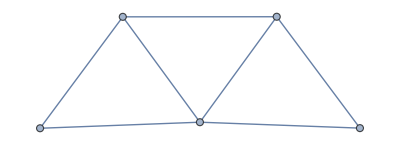

```mathematica
rg
```

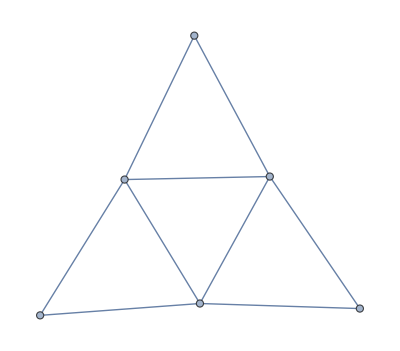

*******************************************************

COMPUTING CONCEPTUAL STRUCTURE: 63 CONCEPTS

*******************************************************

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

$Aborted

```mathematica
rg=RandomGraph[BarabasiAlbertGraphDistribution[6,2]]
cm=AdjacencyMatrix[rg]//Normal;
IIandBDM[cm]//AbsoluteTiming
```

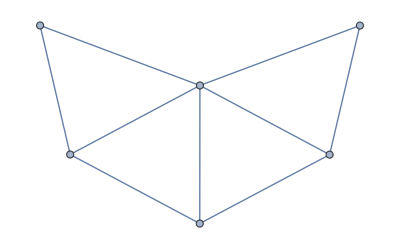

{{0,1,1,1,1,1},{1,0,1,0,0,0},{1,1,0,1,0,0},{1,0,1,0,1,0},{1,0,0,1,0,1},{1,0,0,0,1,0}}

{XOR,XOR,AND,OR,OR,OR}

/Users/beto/Documents/outputs.csv

```mathematica
rg=RandomGraph[BarabasiAlbertGraphDistribution[3,2]]
cm=AdjacencyMatrix[rg]//Normal
dyn=createRandomDynamic[Length[cm]]["Dynamic"]
Export["/Users/beto/Documents/outputs.csv",runDynamic[cm,dyn]["RepertoireOutputs"]]
```

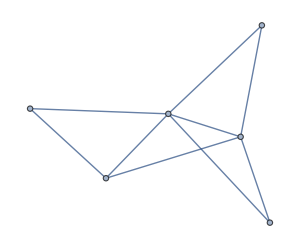

{{0,1,1,0,1,1},{1,0,1,1,1,1},{1,1,0,1,0,0},{0,1,1,0,0,0},{1,1,0,0,0,0},{1,1,0,0,0,0}}

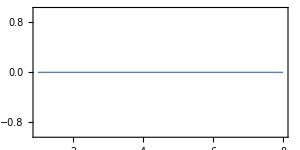
{395.772,<|II→0.6878,BDM→-Graphics-|>}

```mathematica
rg=RandomGraph[BarabasiAlbertGraphDistribution[6,2]]
cm=AdjacencyMatrix[rg]//Normal
IIandBDM[cm]//AbsoluteTiming
```

```mathematica
Export["/Users/beto/Documents/net.csv",EdgeList[rg]]
```

/Users/beto/Documents/net.csv

```mathematica
Export["/Users/beto/Documents/net2.csv",List@@@EdgeList[rg]]
```

/Users/beto/Documents/net2.csv

```mathematica
myiiBDM[noNodes_, noEdges_]:=Module[
{rg,cm,ii,intInf, myBDM},
rg=RandomGraph[BarabasiAlbertGraphDistribution[noNodes,noEdges]];
cm=AdjacencyMatrix[rg]//Normal;
ii=IIandBDM[cm];
intInf = ii["II"];
myBDM = ii["BDM"];
<|"INTEGRATED INFORMATION"->intInf,
"BDM"-> myBDM,
"RG"-> rg
|>

];
```

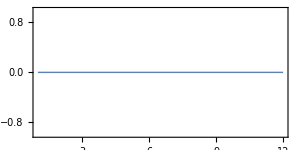
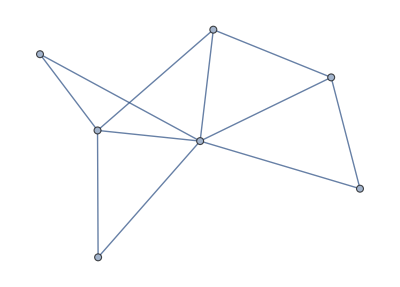
{8219.24,<|INTEGRATED INFORMATION→0.197673,BDM→-Graphics-,RG→-Graphics-|>}

```mathematica
myiiBDM[7,2]//AbsoluteTiming
```

```mathematica
simpleFunc[numNodes_,numEdges_]:=myiiBDM[ToExpression[numNodes],ToExpression[numEdges]];
CloudDeploy[FormFunction[{"number of nodes"->"String","number of edges"->"String"},simpleFunc[#nodes,#pattern]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/eeb0ba03-90fb-489e-8526-cd0ab8cb9bfb]

```mathematica
noNodes=6;
noEdges = 2;
rg=RandomGraph[BarabasiAlbertGraphDistribution[noNodes,noEdges]];
Export["/Users/beto/Documents/01_TopologyNetwork"<>ToString[noNodes]<>".csv",List@@@EdgeList[rg]];

cm=AdjacencyMatrix[rg]//Normal;

fileDynamicsName = "/Users/beto/Documents/02_dynamicsNetwork"<>ToString[noNodes]<>".csv";
dynStr=OpenWrite[fileDynamicsName];
Close[dynStr];

fileiiName = "/Users/beto/Documents/03_iiValuesNetwork"<>ToString[noNodes]<>".csv";
iiStr=OpenWrite[fileiiName];
Close[iiStr];

dynStr=OpenAppend[fileDynamicsName];
iiStr=OpenAppend[fileiiName];

For[i=1,i≤100, i++,
ii=IIandBDM[cm];
dy=ii["Dynamic"];
iiVal = ii["II"];

WriteLine[dynStr,ToString[dy]];
WriteLine[iiStr,ToString[iiVal]];

Print["======================" <> ToString[i]];
Print["Dyn: "<> ToString[dy]];
Print["ii: "<> ToString[iiVal]];


];
Close[dynStr];
Close[iiStr];
```

```mathematica
noNodes=12;
noEdges = 1;
dy={"XOR","AND","XOR","OR","XOR","XOR","OR","AND","XOR","OR","XOR","AND"};

fileDynamicsName = "/Users/beto/Documents/02_dynamicsNetwork"<>ToString[noNodes]<>".csv";
dynStr=OpenWrite[fileDynamicsName];
WriteLine[dynStr,ToString[dy]];
Close[dynStr];

fileiiName = "/Users/beto/Documents/03_iiValuesNetwork"<>ToString[noNodes]<>".csv";
iiStr=OpenWrite[fileiiName];
Close[iiStr];

iiStr=OpenAppend[fileiiName];

For[i=1,i≤2, i++,
rg=RandomGraph[BarabasiAlbertGraphDistribution[noNodes,noEdges]];
cm=AdjacencyMatrix[rg]//Normal;
Export["/Users/beto/Documents/01_TopologyNetwork"<>ToString[noNodes]<>"_"<>ToString[i]<>".csv",List@@@EdgeList[rg]];

ii=IIandBDM[cm,dy]//AbsoluteTiming;
iiVal = ii[[2]]["II"];
myTime = iiVal;
WriteLine[iiStr,ToString[iiVal]];

Print["======================" <> ToString[i]];
Print["Dyn: "<> ToString[dy]];
Print["ii: "<> ToString[iiVal] <> ", Time: "<> ToString[myTime]];
];
Close[iiStr];
```

$Aborted

{XOR,XOR,AND,XOR,OR,AND,XOR,AND}

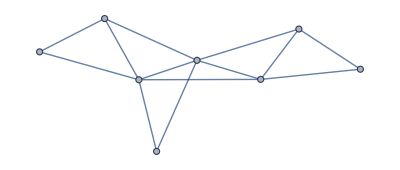

```mathematica
i=6;
noNodes=8;
noEdges = 1;

(*create ands save dynamic*)
(*dy=createRandomDynamic[noNodes]["Dynamic"]*)
dy={"XOR","AND","XOR","OR","XOR","XOR","OR","AND","XOR","OR","XOR","AND"};

fileDynamicsName = "/Users/beto/Documents/02_dynamicsNetwork"<>ToString[noNodes]<>ToString[i]<>".csv";
dynStr=OpenWrite[fileDynamicsName];
WriteLine[dynStr,ToString[dy]];
Close[dynStr];

(*create and save topology*)
rg=RandomGraph[BarabasiAlbertGraphDistribution[noNodes,noEdges]]
EdgeCount[rg]
cm=AdjacencyMatrix[rg]//Normal;
Export["/Users/beto/Documents/01_TopologyNetwork"<>ToString[noNodes]<>ToString[i]<>".csv",List@@@EdgeList[rg]];

(*compute and save ii value*)
ii=IIandBDM[cm,dy];
iiVal = ii["II"]

fileiiName = "/Users/beto/Documents/03_iiValuesNetwork"<>ToString[noNodes]<>".csv";
iiStr=OpenWrite[fileiiName];
WriteLine[iiStr,ToString[iiVal]];
Close[iiStr];
```



{{0,1,1},{1,0,1},{1,1,0}}

```mathematica
rg=RandomGraph[BarabasiAlbertGraphDistribution[3,2]]
(*dy={"XOR","XOR","AND","XOR","OR","AND","XOR","AND"};*)
dy={"XOR","XOR","AND"};
cm=AdjacencyMatrix[rg]//Normal
outs=runDynamic[cm,dy]["RepertoireOutputs"];
outs2=ToString[outs];
outs2=StringReplace[outs2,"{"->"["];
outs2=StringReplace[outs2,"}"->"]"];
Export["/Users/beto/Documents/test2.txt",outs2];
```

```mathematica
createRandomDynamic[12]["Dynamic"]
createSimpleRandomDynamic[12]["Dynamic"]
```

{XOR,OR,XOR,XOR,XOR,XOR,OR,OR,OR,OR,AND,XOR}

createSimpleRandomDynamic[12][Dynamic]

```mathematica
For [i=1,i≤100,i++,
noNodes=8;
noEdges = 2;

(*--Bernoulli*)
(*rg=RandomGraph[DegreeGraphDistribution[ConstantArray[2,12]]];
While[ConnectedGraphQ[rg]===False,rg=RandomGraph[DegreeGraphDistribution[ConstantArray[2,12]]]];*)
(*--FREE SMALL WORLD*)
(*rg=RandomGraph[WattsStrogatzGraphDistribution[noNodes,0.05,2]];*)
(*--ERDOS RENYI NETWORKS*)
(*rg=RandomGraph[{noNodes,12}];
While[ConnectedGraphQ[rrg]===False,rg=RandomGraph[{noNodes,12}]];*)
(*--FREE SCALE NETWORKS*)
rg=RandomGraph[BarabasiAlbertGraphDistribution[noNodes,noEdges]];
(*dy={"XOR","XOR","AND","XOR","OR"};*)
(*dy={"AND","XOR","OR","AND","AND","OR"};*)
(*dy={"XOR","XOR","AND","XOR","OR","AND","OR"};*)
dy={"XOR","XOR","AND","XOR","OR","AND","XOR","AND"};
(*dy={"XOR","XOR","AND","XOR","XOR","AND","XOR","AND","OR"};*)
(*dy={"OR","XOR","AND","OR","AND","AND","XOR","AND","OR","XOR"};*)
(*dy={"OR","OR","OR","OR","AND","OR","XOR","AND","XOR","XOR","AND"};*)
(*dy={"XOR","AND","XOR","OR","XOR","XOR","OR","AND","XOR","OR","XOR","AND"};*)
(*dy={"XOR","AND","XOR","OR","XOR","XOR","OR","AND","XOR","OR","XOR","AND","XOR"};*)

cm=AdjacencyMatrix[rg]//Normal;
outs=runDynamic[cm,dy]["RepertoireOutputs"];

Export["/Users/beto/Documents/"<>ToString[noNodes]<>"Nodes2D/01_TopologyNetwork"<>ToString[noNodes]<>"2D_"<>ToString[i]<>".csv",List@@@EdgeList[rg]];
input=createBinRandomInput[Length[cm]];
cs=calculateOneOutptuOfNetwork[input,cm,dy]["Output"];

outs2=ToString[outs];
outs2=StringReplace[outs2,"{"->"["];
outs2=StringReplace[outs2,"}"->"]"];

cm2=ToString[cm];
cm2=StringReplace[cm2,"{"->"["];
cm2=StringReplace[cm2,"}"->"]"];

cs2=ToString[cs];
cs2=StringReplace[cs2,"{"->"("];
cs2=StringReplace[cs2,"}"->")"];

line= "import pyphi
import numpy as np

tpm=np.array("<>outs2<>")\n"<>

"cm=np.array(" <> cm2<>")\n"<>

"labels=('1','2','3','4','5','6','7','8')\n"<>
"state ="<> cs2<>
"\nnode_indices=(0,1,2,3,4,5,6,7)
network=pyphi.Network(tpm,cm=cm,node_labels=labels)
subsystem=pyphi.Subsystem(network,state,node_indices)
sia=pyphi.compute.sia(subsystem)
phi = sia.phi
file = open(\"sample_"<>ToString[noNodes]<>"2D"<>ToString[i]<>".txt\",\"w\")
file.write(str(phi))
file.close()
";

Export["/Users/beto/Documents/"<>ToString[noNodes]<>"Nodes2D/Scripts"<>ToString[noNodes]<>"2D/scriptLength_"<>ToString[noNodes]<>"2D"<>ToString[i]<>".py",line,"Text"];

bashFileName = "/Users/beto/Documents/"<>ToString[noNodes]<>"Nodes2D/Scripts"<>ToString[noNodes]<>"2D/bash"<>ToString[noNodes]<>"2D"<>".sh";
bashStr=OpenAppend[bashFileName];
WriteLine[bashStr,"python scriptLength_"<>ToString[noNodes]<>"2D"<>ToString[i]<>".py"];
Close[bashStr];

];
```

```mathematica
<|"RepertoireOutputs"->({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {1, 0, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 1, 1, 0}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 1, 1, 0}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 1, 1, 0}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 1, 1, 0}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 1, 1, 0}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 1, 1, 0}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 1, 1, 0}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 1, 1, 0}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 1, 0, 0, 1}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 1, 1, 0}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {1, 0, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 1, 1, 0}, {1, 1, 1, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 1, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 1, 1, 0}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 1, 1, 0}, {1, 1, 1, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 1, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 1, 1, 0}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 1, 1, 0}, {1, 1, 1, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 1, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 1, 1, 0}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 0, 0, 0}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 0, 0, 0, 0}, {0, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 0, 1, 1, 0}, {1, 1, 1, 1, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {1, 1, 0, 1, 1, 0, 0, 1}, {0, 1, 0, 1, 1, 1, 1, 1}, {0, 1, 1, 1, 1, 1, 1, 1}})|>
```

{1,1,0,0,1,0,0,1}

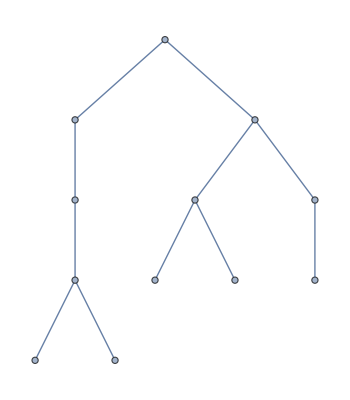

11

```mathematica
rrg=RandomGraph[{12,12}];
While[ConnectedGraphQ[rrg]===False,rrg={};rrg=RandomGraph[{12,11}]]
rrg
EdgeCount[rrg]
```

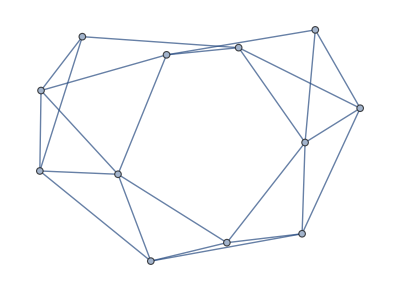

```mathematica
RandomGraph[WattsStrogatzGraphDistribution[12,0.05,2]]
```

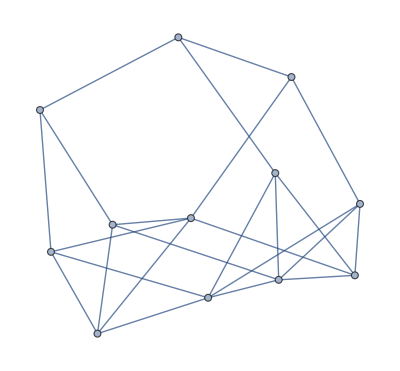

24

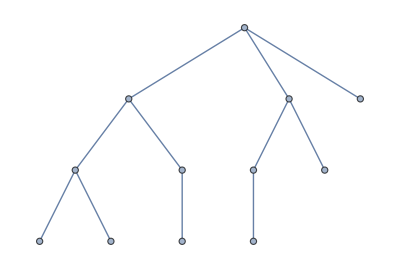

11

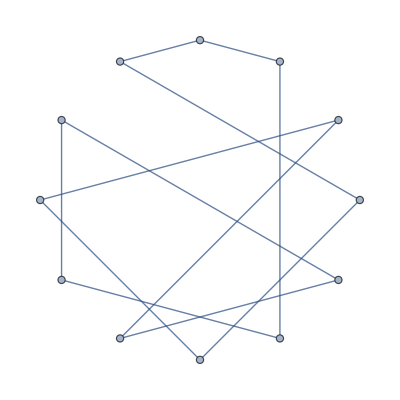

12

```mathematica
rrg=RandomGraph[BernoulliGraphDistribution[12,0.001]];
While[ConnectedGraphQ[rrg]===False,rrg=RandomGraph[BernoulliGraphDistribution[12,0.3]]]

rrg
EdgeCount[rrg]
rg=RandomGraph[BarabasiAlbertGraphDistribution[12,1]]
EdgeCount[rg]


rrg=RandomGraph[DegreeGraphDistribution[ConstantArray[2,12]]];
While[ConnectedGraphQ[rrg]===False,rrg=RandomGraph[DegreeGraphDistribution[ConstantArray[2,12]]]]
rrg
EdgeCount[rrg]
```

```mathematica
ConstantArray[2,12]
```

{2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
ordering files
```

```mathematica
noNodes=7;
SetDirectory["/Users/beto/Documents/Scripts"<>ToString[noNodes]<>"2D"];
For[i=1,i≤ 100, i++,
If[FileExistsQ["sample_"<>ToString[noNodes]<>ToString[i]<>".txt"],

file=Import["sample_"<>ToString[noNodes]<>ToString[i]<>".txt"];

iiValFileName ="/Users/beto/Documents/Scripts"<>ToString[noNodes]<>"2D/iiVal"<>ToString[noNodes]<>".csv";
iiValStr=OpenAppend[iiValFileName];
WriteLine[iiValStr,file];
Close[iiValStr];
];
]
```